# Studying deformation near soft singularity in e^+e^-→γ^*→d d̄

## Resources

```mathematica
RustBindingsPath="/Users/valentin/Documents/MG5/old_madnklk/PLUGIN/pynloop/Mathematica";
AlphaLoopPath="/Users/valentin/Documents/MG5/old_madnklk/PLUGIN/pynloop";
```

```mathematica
Get[RustBindingsPath<>"/"<>"RustFromMathematica.m"]
```

Package for accessing alphaLoop implementation in Rust.

Variables you may want to overwrite are:

RFM$LTDFolder = <Path>;
RFM$PythonInterpreter = <Path>;
RFM$CUBAPath = <Path>;
RFM$SCSPath=<Path>;
RFM$ECOSPath=<Path>;

The function: 
RFM$GetLTDHook[name_,OptionsPattern[
{
RunMode->'LTD',
HyperparametersPath->'LTD/hyperparameters.yaml',
TopologiesPath->'LTD/topologies.yaml',
AmplitudesPath->'LTD/anplitudes.yaml',
DEBUG->False
}

Allows you to generate a hook, which will automatically be placed in the list:

RFM$AllHooksStarted

Then you can test that one hook is active with:

RFM$CheckHookStatus[hook_]

And use them to access information from Rust with the following three API entry points (for now):

RFM$GetLTDDeformation[hook_, RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetCrossSectionDeformation[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetRescaling[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$Parameterize[hook_,LoopIndex_,ECM_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$InvParameterize[hook_,LoopIndex_,ECM_,Momentum_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$Evaluate[hook_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateCut[hook_,CutID_,scalingFactor_, scalingFactorJacobian_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateIntegrand[hook_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]

Specify the LTD folder to the hook package:

```mathematica
RFM$LTDFolder=AlphaLoopPath;
```

Make sure a stat folder exists in the local directory:

```mathematica
If[Not[DirectoryQ[NotebookDirectory[]<>"/stats"]],CreateDirectory[NotebookDirectory[]<>"stats"]];
```

Generic expression of ellipsoids, we will consider the triangle loop graph in k-space (i.e. to the left of the cutkosky cut, so cut_ID=2), with the following momentum routing:

-Graphics-

```mathematica
Ellipsoids[k_,p_,m_,p0_,N_]:=Flatten[Table[{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]<0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]<0},{i, 1,N},{j,i+1,N}]]
```

Clean monofont print

```mathematica
MyPrint[msg_]:=Print[Style[msg,FontFamily->"Monaco"]]
```

Get the hook to various deformation functional choices

First clean up all existing ones

```mathematica
RefreshHooks[]:=Module[{},
RFM$KillAllHooks[];
DeformUVDampenAfterLambda10Hook=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/deform_UV_dampen_after_constant_lambda10.yaml",
DEBUG->False
];
DeformUVDampenAfterLambda10HookSemiInclusive=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/deform_UV_dampen_after_constant_lambda10_semi_inclusive.yaml",
DEBUG->False
];
NoDeformationHook=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/NoDeformation.yaml",
DEBUG->False
];
NoDeformationHookSemiInclusive=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/NoDeformation_semi_inclusive.yaml",
DEBUG->False
];
{RFM$CheckHookStatus[DeformUVDampenAfterLambda10Hook],RFM$CheckHookStatus[DeformUVDampenAfterLambda10HookSemiInclusive],RFM$CheckHookStatus[NoDeformationHook],RFM$CheckHookStatus[NoDeformationHookSemiInclusive]}
]
```

```mathematica
RefreshHooks[]
```

{True,True,True,True}

Set below the desired point density for the heat maps

```mathematica
HeatMapDensity=10;
```

And for the vector fields:

```mathematica
VectorFieldDensity=20;
```

Useful 3D euclidean norm

```mathematica
VDot[k_]:=k⟦1⟧^2+k⟦2⟧^2+k⟦3⟧^2
```

## Ellipsoids and kinematics definition and access functions

```mathematica
Ellipsoids[k_,p_,m_,p0_,N_,OptionsPattern[{Contour->False}]]:=Flatten[Table[
If[OptionValue[Contour],
{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]==0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]==0},
{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]<0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]<0}
],{i, 1,N},{j,i+1,N}]]
```

```mathematica
TriangleP1={0,0,0};
TriangleP10=2.0;
TriangleP2={N[1/Sqrt[2],16],N[1/Sqrt[2],16],0};
TriangleP20=Sqrt[VDot[TriangleP2]];
```

Apply rescaling

```mathematica
GetRescaling[l_]:=Block[{RescalingSolutions},
RescalingSolutions=RFM$GetRescaling[DeformUVDampenAfterLambda10Hook,2,{{0,0,0},l}];
If[RescalingSolutions["tSolutions"]⟦1⟧>0,
{RescalingSolutions["tSolutions"]⟦1⟧,RescalingSolutions["tJacobians"]⟦1⟧},
{RescalingSolutions["tSolutions"]⟦2⟧,RescalingSolutions["tJacobians"]⟦2⟧}
]
]
```

```mathematica
RescalingFactor=GetRescaling[TriangleP2]⟦1⟧;
RescalingJacobian=GetRescaling[TriangleP2]⟦2⟧;
TriangleP2*= RescalingFactor;
TriangleP20*=RescalingFactor;
SoftPoint=TriangleP2*RescalingFactor;
```

Now that the kinematics is set, generate all ellipsoids

```mathematica
AllTriangleEllipsoids=Ellipsoids[{kx,ky,0},{TriangleP1,TriangleP1+TriangleP2,0},{0,0,0},{TriangleP10,TriangleP10+TriangleP20,0},3,Contour->False];
AllTriangleEllipsoidsContour=Ellipsoids[{kx,ky,0},{TriangleP1,TriangleP1+TriangleP2,0},{0,0,0},{TriangleP10,TriangleP10+TriangleP20,0},3,Contour->True];
```

And define functions accessing the deformation for the particular case of interest

```mathematica
GetDeformationVector[kx_?NumberQ,ky_?NumberQ,kz_?NumberQ,OptionsPattern[{hook->DeformUVDampenAfterLambda10Hook,cutID->2}]]:=Block[{DeformedMomenta},
DeformedMomenta=RFM$GetCrossSectionDeformation[OptionValue[hook],OptionValue[cutID],{{kx,ky,kz},TriangleP2/RescalingFactor},DEBUG->False];
Im[-DeformedMomenta["DeformedMomenta"]]
]
```

```mathematica
GetDeformationVectorXY[kx_?NumericQ,ky_?NumberQ]:=Block[
{Kappas},
Kappas=GetDeformationVector[kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor];
{Kappas⟦1⟧⟦2⟧,Kappas⟦1⟧⟦3⟧}
]
```

```mathematica
EvaluateCutXY[hook_,kx_?NumericQ,ky_?NumberQ,OptionsPattern[{DEBUG->False,CUTID->2}]]:=Block[
{},
If[OptionValue[DEBUG],Print["kx="<>ToString[kx,InputForm]<>" "<>"ky="<>ToString[ky,InputForm]];];
RFM$EvaluateCut[hook,OptionValue[CUTID],RescalingFactor,RescalingJacobian,{{kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor},TriangleP2/RescalingFactor},DEBUG->False,f128->False]
]
```

```mathematica
EvaluateFullXY[hook_,kx_?NumericQ,ky_?NumberQ,OptionsPattern[DEBUG->False]]:=Block[
{invParametrizeK,invParametrizeL},
If[OptionValue[DEBUG],Print["kx="<>ToString[kx,InputForm]<>" "<>"ky="<>ToString[ky,InputForm]];];
invParametrizeK=RFM$InvParameterize[hook,0,2,{kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor},DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum k = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeK}]]]];
invParametrizeL=RFM$InvParameterize[hook,1,2,TriangleP2/RescalingFactor,DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum l = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeL}]]]];
RFM$EvaluateIntegrand[hook,Join[invParametrizeK,invParametrizeL],DEBUG->OptionValue[DEBUG]]
]
```

## Zoomed-in visualisations

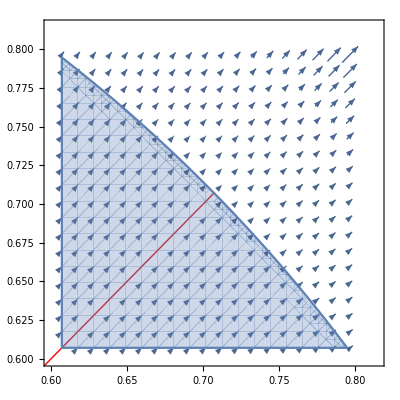

```mathematica
ZoomedInDeformation=Block[{ZoomDelta},
ZoomDelta=0.1;
Show[
VectorPlot[GetDeformationVectorXY[kx,ky],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
VectorPoints->VectorFieldDensity],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
RegionPlot[
AllTriangleEllipsoids[[3]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
Axes->False,
Frame->True,
ImagePadding->1
]
]
]
```

```mathematica
ZoomedInDeformationContour=Block[{ZoomDelta},
ZoomDelta=0.1;
Show[
VectorPlot[GetDeformationVectorXY[kx,ky],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
VectorPoints->VectorFieldDensity],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
Axes->False,
Frame->True,
ImagePadding->1
]
]
];
```

```mathematica
ZoomedInNoDeformationContour=Block[{ZoomDelta},
ZoomDelta=0.1;
Show[
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
Axes->False,
Frame->True,
ImagePadding->1
],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}]
]
];
```

```mathematica
MyReDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Re[EvaluateCutXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyImDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Im[EvaluateCutXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

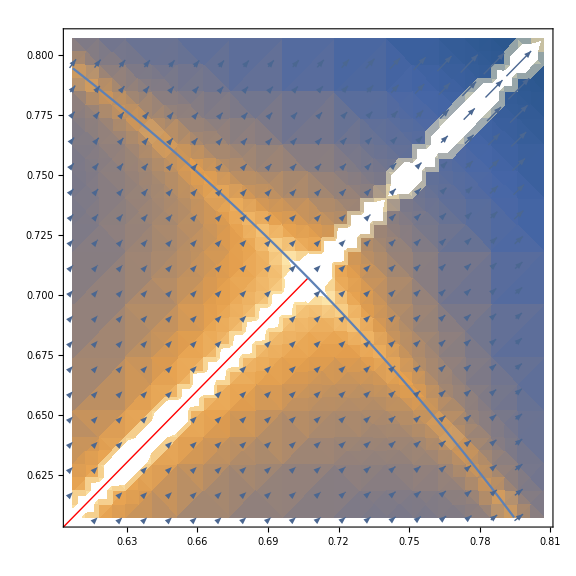
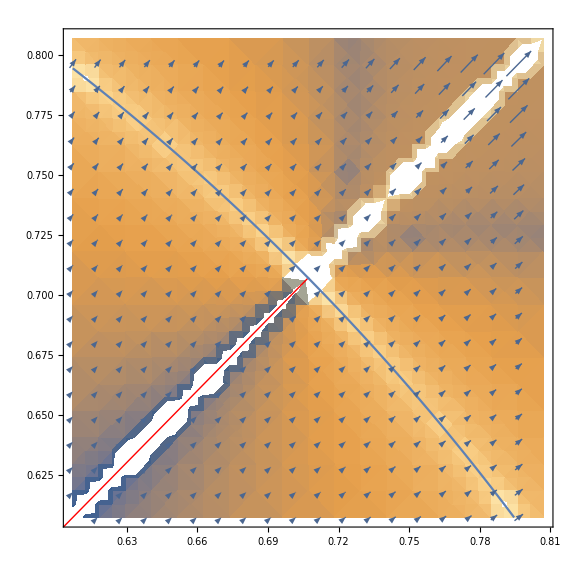
-Graphics-Im[(LTD^2@cut2] | -Graphics-Re[LTD^2@cut2]

```mathematica
Grid[{{
Labeled[Show[MyReDensityPlot,ZoomedInDeformationContour,ImageSize->Large],"Im[(LTD^2@cut2]"],
Labeled[Show[MyImDensityPlot,ZoomedInDeformationContour,ImageSize->Large],"Re[LTD^2@cut2]"]
}}]
```

```mathematica
MyFullEvalReDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Re[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyFullEvalImDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Im[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

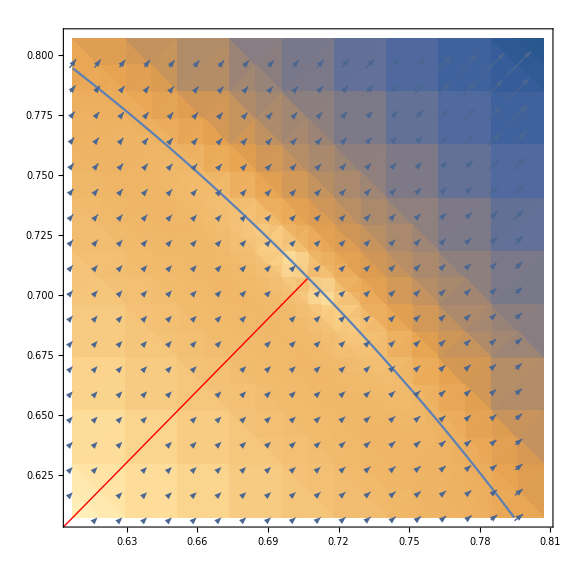
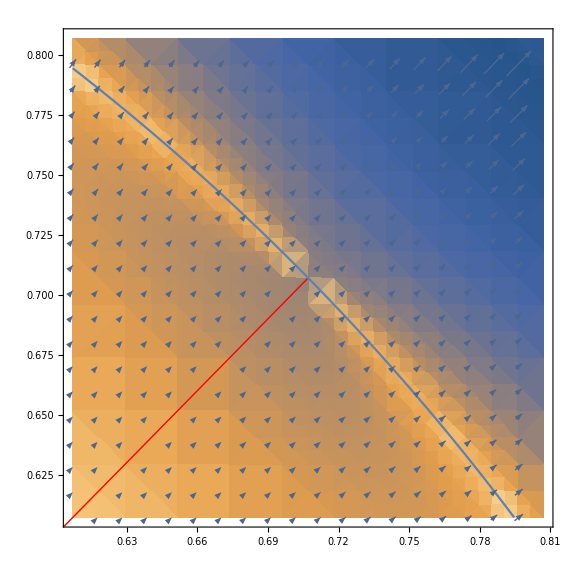
-Graphics-Im[LTD^2@full] | -Graphics-Re[LTD^2@full]

```mathematica
Grid[{{
Labeled[Show[MyFullEvalReDensityPlot,ZoomedInDeformationContour,ImageSize->Large],"Im[LTD^2@full]"],
Labeled[Show[MyFullEvalImDensityPlot,ZoomedInDeformationContour,ImageSize->Large],"Re[LTD^2@full]"]
}}]
```

```mathematica
MyFullEvalReNoDeformationDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Re[EvaluateFullXY[NoDeformationHook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

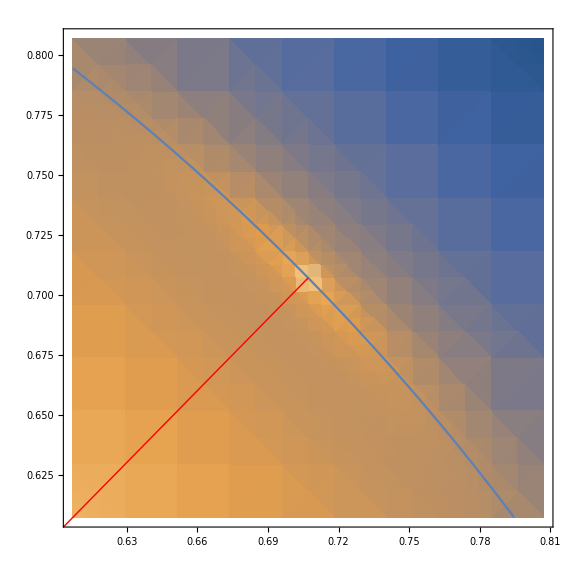
-Graphics-Re[LTD^2@full] with no deformation

```mathematica
Labeled[Show[MyFullEvalReNoDeformationDensityPlot,ZoomedInNoDeformationContour,ImageSize->Large],"Re[LTD^2@full] with no deformation"]
```

Now plot the size of the deformation

```mathematica
MyDeformationNormPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Abs[Norm[GetDeformationVectorXY[kx,ky]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

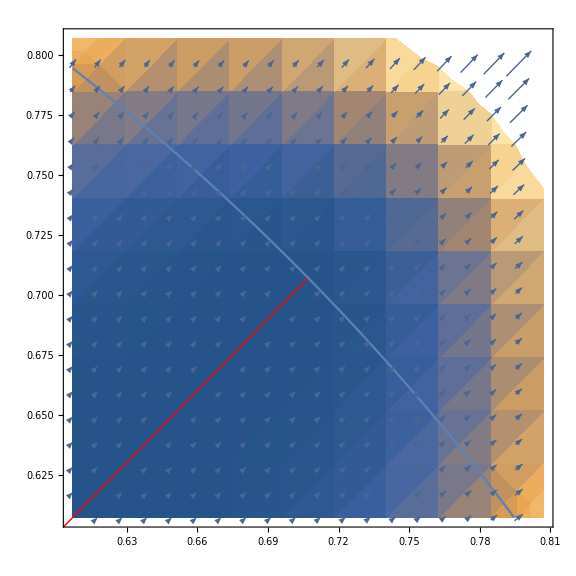
-Graphics-|κLTD^2|

```mathematica
Labeled[Show[MyDeformationNormPlot,ZoomedInDeformationContour,ImageSize->Large],"|κLTD^2|"]
```

Finally let’s look at the integrand in the presence of a selector 0.4 < pt(jet1)< 0.8:

```mathematica
MyFullEvalReDensityPlotSemiInclusive=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Re[EvaluateFullXY[DeformUVDampenAfterLambda10HookSemiInclusive,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyFullEvalImDensityPlotSemiInclusive=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Im[EvaluateFullXY[DeformUVDampenAfterLambda10HookSemiInclusive,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
Grid[{{
Labeled[Show[MyFullEvalReDensityPlotSemiInclusive,ZoomedInDeformationContour,ImageSize->Large],"Im[LTD^2@full]"],
Labeled[Show[MyFullEvalImDensityPlotSemiInclusive,ZoomedInDeformationContour,ImageSize->Large],"Re[LTD^2@full]"]
}}]
```

-Graphics-Im[LTD^2@full] | -Graphics-Re[LTD^2@full]

## Zoomed-out visualisations

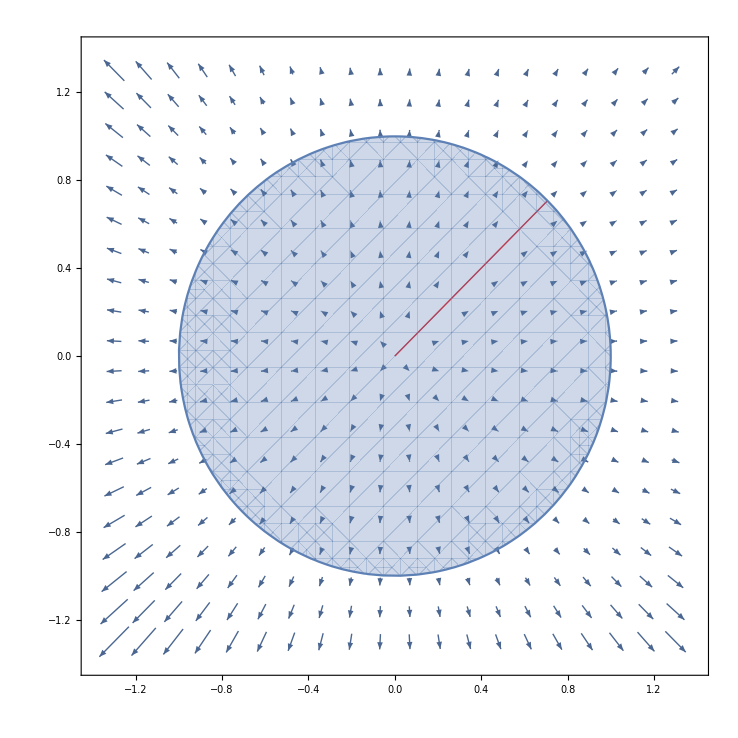

```mathematica
ZoomedOutDeformation=Show[
VectorPlot[GetDeformationVectorXY[kx,ky],{kx,-1.3,1.3},{ky,-1.3,1.3},VectorPoints->VectorFieldDensity],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
RegionPlot[
AllTriangleEllipsoids[[3]],{kx,-1,2},{ky,-1,2},
Axes->False,
Frame->True,
ImagePadding->1
]
]
```

```mathematica
ZoomedOutDeformationContour=Show[
VectorPlot[GetDeformationVectorXY[kx,ky],{kx,-1.3,1.3},{ky,-1.3,1.3},VectorPoints->VectorFieldDensity],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],{kx,-1,2},{ky,-1,2},
Axes->False,
Frame->True,
ImagePadding->1
]
];
```

```mathematica
ZoomedOutNoDeformationContour=Show[
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],{kx,-1.3,1.3},{ky,-1.3,1.3},
Axes->False,
Frame->True,
ImagePadding->1
],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}]
];
```

```mathematica
MyFullEvalReDensityPlotZoomedOut=Block[
{},
DensityPlot[Log[Abs[Re[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyFullEvalImDensityPlotZoomedOut=Block[
{},
DensityPlot[Log[Abs[Im[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

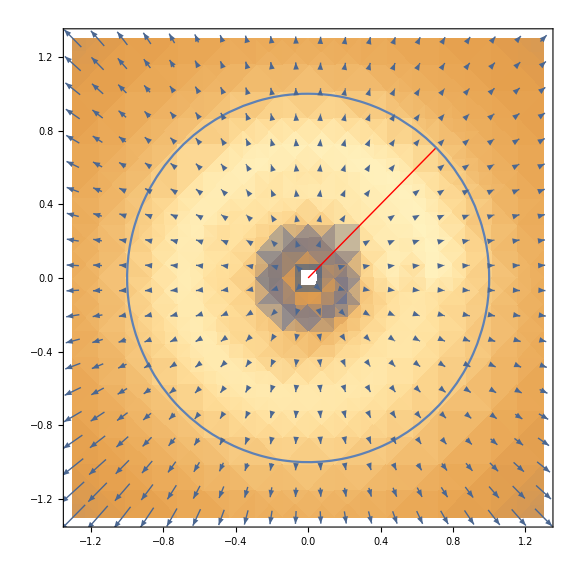
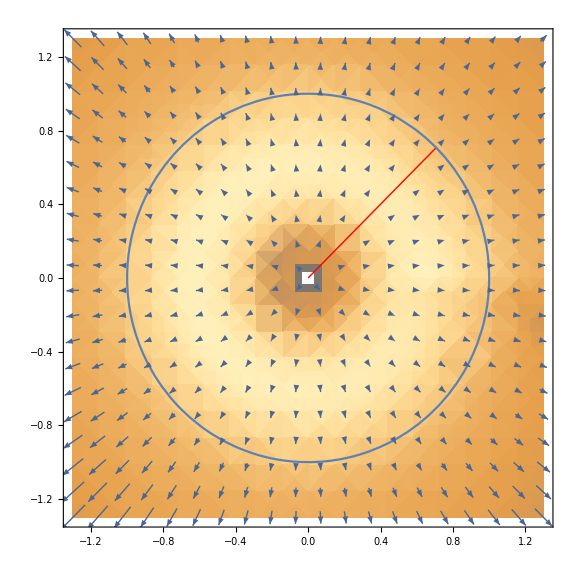
-Graphics-Im[LTD^2@full] | -Graphics-Re[LTD^2@full]

```mathematica
Grid[{{
Labeled[Show[MyFullEvalReDensityPlotZoomedOut,ZoomedOutDeformationContour,ImageSize->Large],"Im[LTD^2@full]"],
Labeled[Show[MyFullEvalImDensityPlotZoomedOut,ZoomedOutDeformationContour,ImageSize->Large],"Re[LTD^2@full]"]
}}]
```

```mathematica
MyFullEvalReNoDeformationDensityPlotZoomedOut=Block[
{},
DensityPlot[Log[Abs[Re[EvaluateFullXY[NoDeformationHook,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

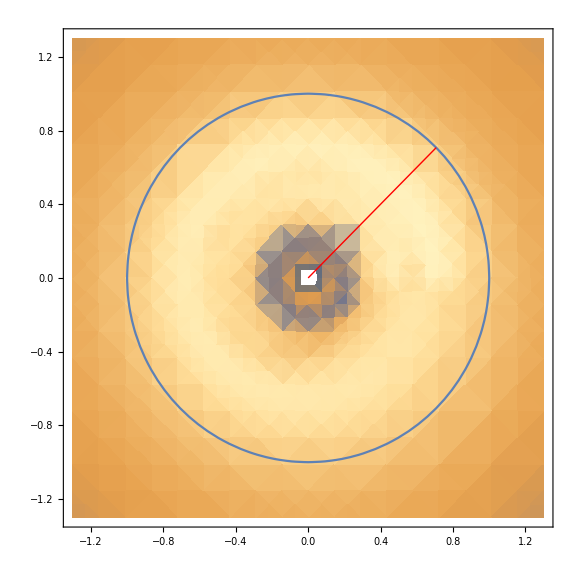
-Graphics-Re[LTD^2@full] with no deformation

```mathematica
Labeled[Show[MyFullEvalReNoDeformationDensityPlotZoomedOut,ZoomedOutNoDeformationContour,ImageSize->Large],"Re[LTD^2@full] with no deformation"]
```

Now the semi-inclusive integrand in the region 0.4 < pt(j1) < 0.8

```mathematica
MyFullEvalReDensityPlotZoomedOutSemiInclusive=Block[
{},
DensityPlot[Log[Abs[Re[EvaluateFullXY[DeformUVDampenAfterLambda10HookSemiInclusive,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyFullEvalImDensityPlotZoomedOutSemiInclusive=Block[
{},
DensityPlot[Log[Abs[Im[EvaluateFullXY[DeformUVDampenAfterLambda10HookSemiInclusive,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->HeatMapDensity,Axes->False,
Frame->True,
ImagePadding->1]
];
```

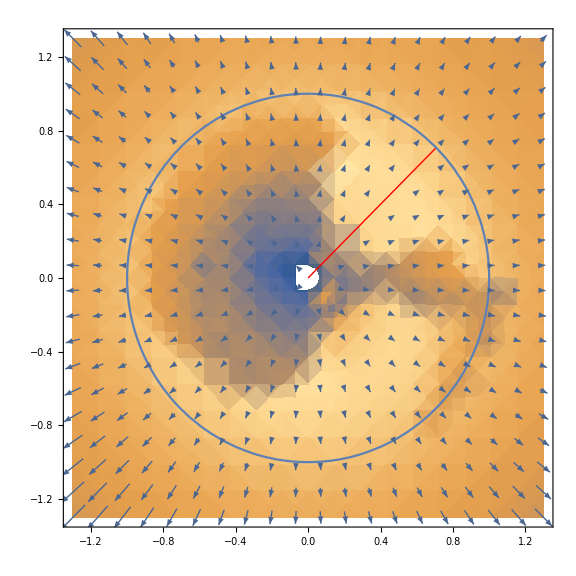
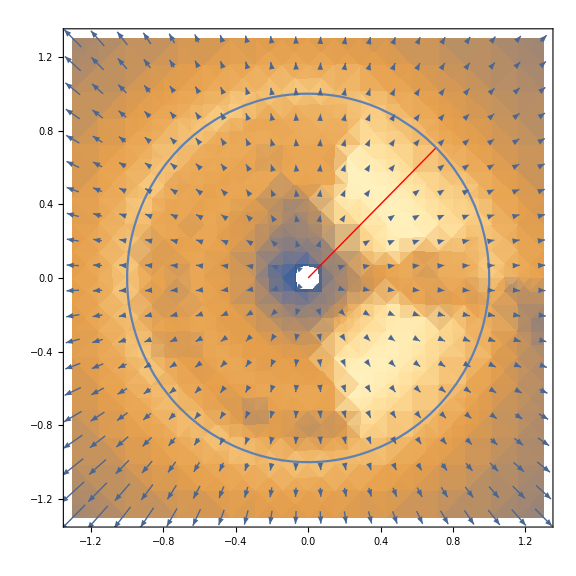
-Graphics-Im[LTD^2@full] | -Graphics-Re[LTD^2@full]

```mathematica
Grid[{{
Labeled[Show[MyFullEvalReDensityPlotZoomedOutSemiInclusive,ZoomedOutDeformationContour,ImageSize->Large],"Im[LTD^2@full]"],
Labeled[Show[MyFullEvalImDensityPlotZoomedOutSemiInclusive,ZoomedOutDeformationContour,ImageSize->Large],"Re[LTD^2@full]"]
}}]
```

Highlight cancellation between positive (green) and negative (red) parts:

```mathematica
MyFullEvalReDensityPlotZoomedOutSemiInclusiveRedGreen=Block[
{},
DensityPlot[Sign[Re[EvaluateFullXY[DeformUVDampenAfterLambda10HookSemiInclusive,kx,ky,DEBUG->False]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*)10,Axes->False,PlotRange->All,
ColorFunction->(If[#>0.,Green,Red]&),ColorFunctionScaling->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyFullEvalImDensityPlotZoomedOutSemiInclusiveRedGreen=Block[
{},
DensityPlot[Sign[Im[EvaluateFullXY[DeformUVDampenAfterLambda10HookSemiInclusive,kx,ky,DEBUG->False]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 10,Axes->False,PlotRange->All,
ColorFunction->(If[#>0.,Green,Red]&),ColorFunctionScaling->False,
Frame->True,
ImagePadding->1]
];
```

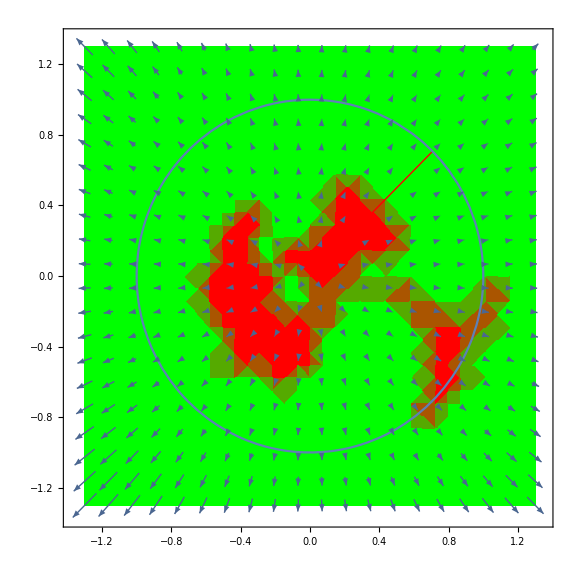
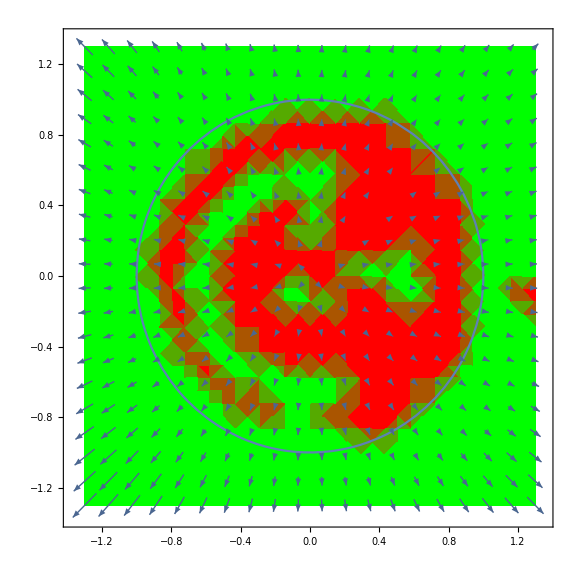
-Graphics-Re[LTD^2@full] | -Graphics-Im[LTD^2@full]

```mathematica
Grid[{{
Labeled[Show[MyFullEvalReDensityPlotZoomedOutSemiInclusiveRedGreen,ZoomedOutDeformationContour,ImageSize->Large],"Re[LTD^2@full]"],
Labeled[Show[MyFullEvalImDensityPlotZoomedOutSemiInclusiveRedGreen,ZoomedOutDeformationContour,ImageSize->Large],"Im[LTD^2@full]"]
}}]
```

## Studying the non-local cancelation of E-surfaces

Common resources beloow

```mathematica
Pt[mom_]:=Sqrt[mom⟦1⟧^2+mom⟦2⟧^2];
```

```mathematica
ScannedMomentum[ky_]:={0,ky,N[1/Sqrt[2],16]};
```

```mathematica
CutLowerBounds=Sort[Table[ky/.sol,{sol,Solve[Pt[ScannedMomentum[ky]] 1/Sqrt[VDot[ScannedMomentum[ky]]]==0.4,ky]}]]
```

{-0.308607,0.308607}

```mathematica
CutUpperBounds=Sort[Table[ky/.sol,{sol,Solve[Pt[ScannedMomentum[ky]] 1/Sqrt[VDot[ScannedMomentum[ky]]]==0.8,ky]}]]
```

{-0.942809,0.942809}

```mathematica
MakeALabeledPoint[location_,label_]:=Block[{},
{Graphics[{PointSize->0.01,Red, Point[location]}],Graphics[{Red,FontSize->15,Text[label,location+{0.1,-0.01}]}]}
]
```

### First varying the same component y for both K and L

Now let’s highlight in this fashion E-surface cancellation, and their non-locality in the presence of a cut, which we shall do by plotting things for cut2 and cut3 (corresponding to the triangle on the right of the Cutkosky Cut, respectively left of it).

For this we will, consider 2D plots where we vary k_y and l_y in k=(0,ky,1/Sqrt[2]) and l=(0,ly,1/Sqrt[2]).

And define functions accessing the deformation for the particular case of interest

```mathematica
EvaluateCutForKLScan[hook_,kComp_?NumericQ,lComp_?NumberQ,OptionsPattern[{DEBUG->False,cutID->2}]]:=Block[
{kvec,lvec, rescaling,rescalingSelected},
kvec=If[OptionValue[cutID]==2,ScannedMomentum[kComp],ScannedMomentum[kComp]];
lvec=If[OptionValue[cutID]==2,ScannedMomentum[lComp],ScannedMomentum[lComp]];
rescaling=RFM$GetRescaling[hook,OptionValue[cutID],{kvec,lvec}];
rescalingSelected=If[rescaling["tSolutions"]⟦1⟧>0,
{rescaling["tSolutions"]⟦1⟧,rescaling["tJacobians"]⟦1⟧},
{rescaling["tSolutions"]⟦2⟧,rescaling["tJacobians"]⟦2⟧}
];
If[OptionValue[DEBUG],Print["Rescaling="<>ToString[rescalingSelected⟦1⟧,InputForm]]];
(* We could evaluate the cuts ourselves too *)
If[OptionValue[DEBUG],Print["Pt(k)="<>ToString[Pt[kvec],InputForm]]];
If[OptionValue[DEBUG],Print["Pt(l)="<>ToString[Pt[lvec],InputForm]]];
(*If[OptionValue[cutID]==1&&Not[0.4<Pt[kvec]<0.8],Return[0.]];*)
(*If[OptionValue[cutID]==2&&Not[0.4<Pt[lvec]<0.8],Return[0.]];*)
RFM$EvaluateCut[hook,OptionValue[cutID],rescalingSelected⟦1⟧,rescalingSelected⟦2⟧,{kvec,lvec},DEBUG->OptionValue[DEBUG],f128->False]
]
```

```mathematica
EvaluateFullForKLScan[hook_,kComp_?NumericQ,lComp_?NumberQ,OptionsPattern[{DEBUG->False,ECM->TriangleP10}]]:=Block[
{kvec,lvec,invParametrizeK,invParametrizeL},
kvec=ScannedMomentum[kComp];
lvec=ScannedMomentum[lComp];
invParametrizeK=RFM$InvParameterize[hook,0,OptionValue[ECM]^2,kvec,DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum k = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeK}]]]];
invParametrizeL=RFM$InvParameterize[hook,1,OptionValue[ECM]^2,lvec,DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum l = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeL}]]]];
RFM$EvaluateIntegrand[hook,Join[invParametrizeK,invParametrizeL],DEBUG->OptionValue[DEBUG]]
]
```

```mathematica
EvaluateCutForKLScan[DeformUVDampenAfterLambda10HookSemiInclusive,N[1/Sqrt[2]],0.6,cutID->1,DEBUG->True]
```

Rescaling=1.

Pt(k)=0.7071067811865475

Pt(l)=0.6

Raw intput sent: evaluate_cut 1 1. 0.5 0 0.7071067811865475 0.7071067811865475 0 0.6 0.7071067811865475

Raw output received: -1.0199794503190973e+04 -1.2442108648300749e+00

-10199.8-1.24421 ⅈ

```mathematica
Table[EvaluateCutForKLScan[DeformUVDampenAfterLambda10HookSemiInclusive,0.3,N[1/Sqrt[2]],cutID->cut,DEBUG->False],{cut,Range[0,3]}]
```

{44.1495+0. ⅈ,0.+0. ⅈ,-170.169+0.8547 ⅈ,44.1495+0. ⅈ}

```mathematica
EvaluateFullForKLScan[DeformUVDampenAfterLambda10Hook,0.5,1.0]
```

4.73747-0.00372092 ⅈ

```mathematica
AllThresholdLinesForKLScanInLxB=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦1⟧,-1.3},{CutUpperBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦1⟧,-1.3},{CutLowerBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦2⟧,-1.3},{CutLowerBounds⟦2⟧,1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦2⟧,-1.3},{CutUpperBounds⟦2⟧,1.3}}]}
}];
```

```mathematica
AllThresholdLinesForKLScanInBxL=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{-1.3,CutUpperBounds⟦1⟧},{1.3,CutUpperBounds⟦1⟧}}]},
{Blue,Thick,Line[{{-1.3,CutLowerBounds⟦1⟧},{1.3,CutLowerBounds⟦1⟧}}]},
{Blue,Thick,Line[{{-1.3,CutLowerBounds⟦2⟧},{1.3,CutLowerBounds⟦2⟧}}]},
{Blue,Thick,Line[{{-1.3,CutUpperBounds⟦2⟧},{1.3,CutUpperBounds⟦2⟧}}]}
}];
```

```mathematica
KLScanDensityPlotCut1Re=Block[
{},
DensityPlot[Sign[Re[EvaluateCutForKLScan[DeformUVDampenAfterLambda10HookSemiInclusive,ky,ly,cutID->1,DEBUG->False]]],
{ky,-1.3,1.3},
{ly,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 10,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_y"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

```mathematica
KLScanDensityPlotCut1Im=Block[
{},
DensityPlot[Sign[Im[EvaluateCutForKLScan[DeformUVDampenAfterLambda10HookSemiInclusive,ky,ly,cutID->1,DEBUG->False]]],
{ky,-1.3,1.3},
{ly,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 10,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_y"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

```mathematica
KLScanDensityPlotCut2Re=Block[
{},
DensityPlot[Sign[Re[EvaluateCutForKLScan[DeformUVDampenAfterLambda10HookSemiInclusive,ky,ly,cutID->2,DEBUG->False]]],
{ky,-1.3,1.3},
{ly,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 10,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_y"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

```mathematica
KLScanDensityPlotCut2Im=Block[
{},
DensityPlot[Sign[Im[EvaluateCutForKLScan[DeformUVDampenAfterLambda10HookSemiInclusive,ky,ly,cutID->2,DEBUG->False]]],
{ky,-1.3,1.3},
{ly,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 10,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_y"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

$Aborted

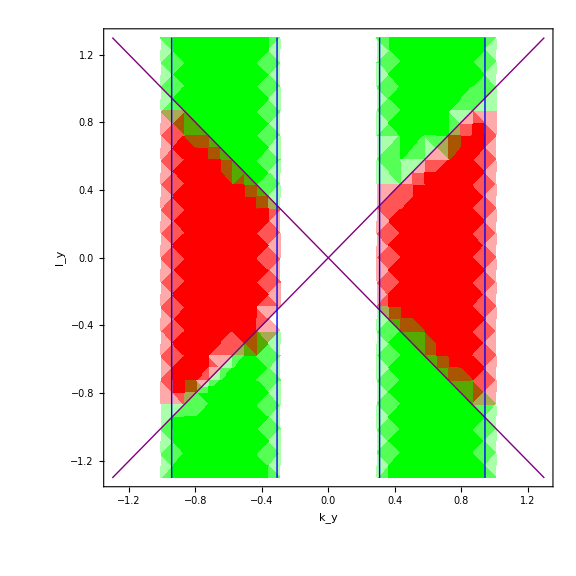
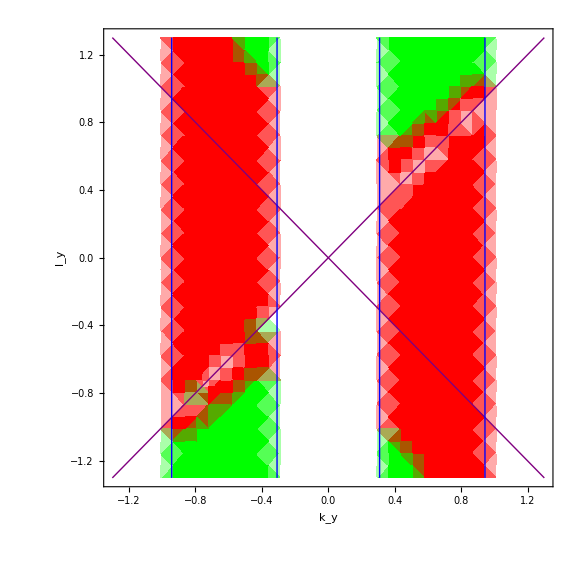
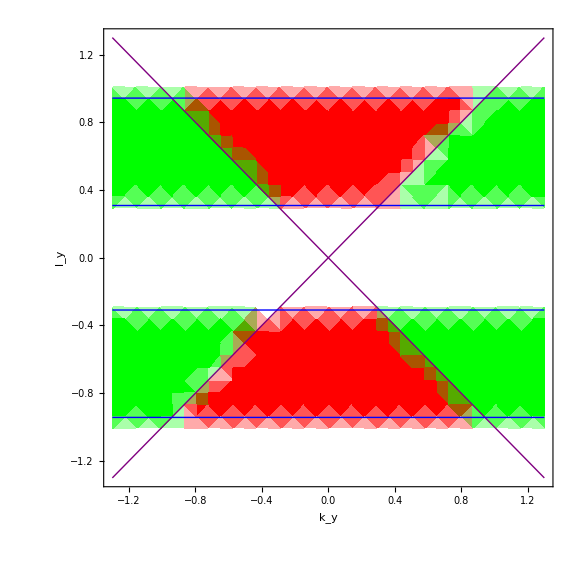
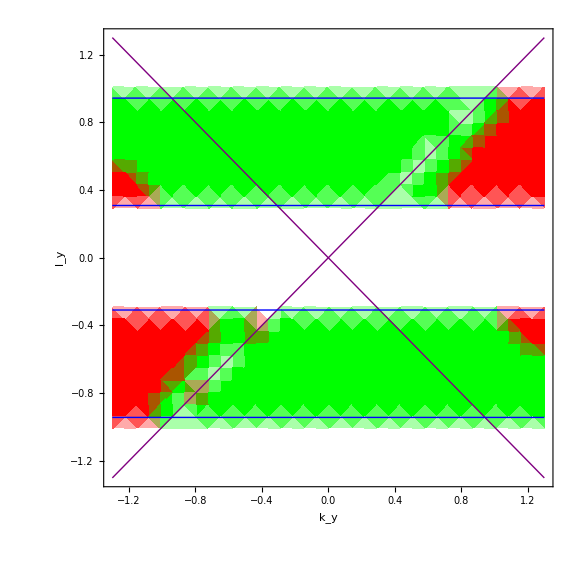
-Graphics-Re[LxB( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )] | -Graphics-Im[LxB( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )]
-Graphics-Im[BxL( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )] | -Graphics-Im[BxL( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )]

```mathematica
Grid[{
{
Labeled[Show[KLScanDensityPlotCut1Re,AllThresholdLinesForKLScanInLxB,ImageSize->Large],"Re[LxB( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )]"],
Labeled[Show[KLScanDensityPlotCut1Im,AllThresholdLinesForKLScanInLxB,ImageSize->Large],"Im[LxB( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )]"]
},
{
Labeled[Show[KLScanDensityPlotCut2Re,AllThresholdLinesForKLScanInBxL,ImageSize->Large],"Im[BxL( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )]"],
Labeled[Show[KLScanDensityPlotCut2Im,AllThresholdLinesForKLScanInBxL,ImageSize->Large],"Im[BxL( ( 0, k_y , 1/(√2)), (0 , l_y ,1/(√2)) )]"]
}
},ItemSize->{50,35}]
```

### Now vary the y component of K the z component of L

Now let’s highlight in this fashion E-surface cancellation, and their non-locality in the presence of a cut, which we shall do by plotting things for cut2 and cut3 (corresponding to the triangle on the right of the Cutkosky Cut, respectively left of it).

For this we will, consider 2D plots where we vary k_y and l_y in k=(0,ky,1/Sqrt[2]) and l=(0,ly,1/Sqrt[2]).

```mathematica
ScannedMomentumK[ky_]:={0,ky,N[1/Sqrt[2],16]};
ScannedMomentumL[lz_]:={0,N[1/Sqrt[2],16],lz};
```

```mathematica
CutBoundsInL=Sort[Table[lz/.sol,{sol,Solve[Pt[ScannedMomentumL[lz]]/Sqrt[VDot[ScannedMomentumL[lz]]]==0.8,lz]}]]
```

{-0.53033,0.53033}

And define functions accessing the deformation for the particular case of interest

```mathematica
EvaluateCutForKLScanYZ[hook_,kComp_?NumericQ,lComp_?NumberQ,
OptionsPattern[{DEBUG->False,cutID->2, RotatedBasis->False,IncludeJacobian->False,ECM->TriangleP10}]]:=Block[
{kvec,lvec, rescaling,rescalingSelected,jacobian=1.,lvecTMP,kvecTMP},
kvec=If[OptionValue[cutID]==2,ScannedMomentumK[kComp],ScannedMomentumK[kComp]];
lvec=If[OptionValue[cutID]==2,ScannedMomentumL[lComp],ScannedMomentumL[lComp]];
rescaling=RFM$GetRescaling[hook,OptionValue[cutID],{kvec,lvec}];
rescalingSelected=If[rescaling["tSolutions"]⟦1⟧>0,
{rescaling["tSolutions"]⟦1⟧,rescaling["tJacobians"]⟦1⟧},
{rescaling["tSolutions"]⟦2⟧,rescaling["tJacobians"]⟦2⟧}
];
If[OptionValue[IncludeJacobian],
kvecTMP=kvec;
If[OptionValue[RotatedBasis],
lvecTMP=lvec-kvec;,
lvecTMP=lvec;
];
jacobian=(RFM$InvParameterize[hook,0,OptionValue[ECM]^2,kvecTMP,DEBUG->OptionValue[DEBUG]]["Jacobian"]*
RFM$InvParameterize[hook,1,OptionValue[ECM]^2,lvecTMP,DEBUG->OptionValue[DEBUG]]["Jacobian"])
]; 
If[And[OptionValue[DEBUG],OptionValue[IncludeJacobian]],MyPrint["Jacobian="<>ToString[jacobian,InputForm]]];
If[OptionValue[DEBUG],MyPrint["Rescaling="<>ToString[rescalingSelected⟦1⟧,InputForm]]];
(* We could evaluate the cuts ourselves too *)
If[OptionValue[DEBUG],MyPrint["Pt(k)="<>ToString[Pt[kvec],InputForm]]];
If[OptionValue[DEBUG],MyPrint["Pt(l)="<>ToString[Pt[lvec],InputForm]]];
(*If[OptionValue[cutID]==1&&Not[0.4<Pt[kvec]<0.8],Return[0.]];*)
(*If[OptionValue[cutID]==2&&Not[0.4<Pt[lvec]<0.8],Return[0.]];*)
(1.0/jacobian)*RFM$EvaluateCut[hook,OptionValue[cutID],rescalingSelected⟦1⟧,rescalingSelected⟦2⟧,{kvec,lvec},DEBUG->OptionValue[DEBUG],f128->False]
]
```

```mathematica
EvaluateFullForKLScanYZ[hook_,kComp_?NumericQ,lComp_?NumberQ,OptionsPattern[{DEBUG->False,ECM->TriangleP10, RotatedBasis->False,IncludeJacobian->False}]]:=Block[
{kvec,lvec,invParametrizeK,JacobianK,invParametrizeL,JacobianL,invP,res},
kvec=ScannedMomentumK[kComp];
lvec=ScannedMomentumL[lComp];
If[OptionValue[RotatedBasis],
lvec=lvec-kvec;
];
invP=RFM$InvParameterize[hook,0,OptionValue[ECM]^2,kvec,DEBUG->OptionValue[DEBUG]];
invParametrizeK=invP["Xs"];
JacobianK=invP["Jacobian"];
If[OptionValue[DEBUG],Print["Xs for loop momentum k = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeK}]]]];
invP=RFM$InvParameterize[hook,1,OptionValue[ECM]^2,lvec,DEBUG->OptionValue[DEBUG]];
invParametrizeL=invP["Xs"];
JacobianL=invP["Jacobian"];
If[OptionValue[DEBUG],Print["Xs for loop momentum l = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeL}]]]];
res=RFM$EvaluateIntegrand[hook,Join[invParametrizeK,invParametrizeL],DEBUG->OptionValue[DEBUG]];
If[Not[OptionValue[IncludeJacobian]],res JacobianK JacobianL,res]
]
```

```mathematica
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,N[1/Sqrt[2]],N[1/Sqrt[2]]+0.002,cutID->1,DEBUG->True,RotatedBasis->True,IncludeJacobian->True]
```

kvecTMP={0, 0.7071067811865475, 0.70710678118654752440084436210484070353`16.}

lvecTMP={0, 1.1102230246251565*^-16, 0.0019999999999998908}

Raw intput sent: inv_parameterize 1 4. 0 0.0000000000000001110223024625157 0.001999999999999891

Raw output received: 9.9273193771708266e+03 9.9900099900094479e-04 2.5000000000000000e-01 1.0000000000000000e+00

lvecJac=9927.319377170827

Raw intput sent: inv_parameterize 0 4. 0 0.7071067811865475 0.7071067811865475

Raw output received: 1.7683882565766151e-02 3.3333333333333331e-01 2.5000000000000000e-01 8.5355339059327373e-01

Raw intput sent: inv_parameterize 1 4. 0 0.0000000000000001110223024625157 0.001999999999999891

Raw output received: 9.9273193771708266e+03 9.9900099900094479e-04 2.5000000000000000e-01 1.0000000000000000e+00

Jacobian=175.55355005874367

Rescaling=1.

Pt(k)=0.7071067811865475

Pt(l)=1.1102230246251565*^-16

Raw intput sent: evaluate_cut 1 1. 0.5 0 0.7071067811865475 0.7071067811865475 0 0.0000000000000001110223024625157 0.001999999999999891

Raw output received: -4.4392334723397644e+03 -1.0286741577997038e-02

-25.2871-0.000058596 ⅈ

```mathematica
RFM$InvParameterize[NoDeformationHookSemiInclusive,0,2,{0.,N[1/Sqrt[2]],N[1/Sqrt[2]]},DEBUG->False]
```

<|Xs→{0.414214,0.25,0.853553},Jacobian→0.0193087|>

```mathematica
Table[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,0.3,N[1/Sqrt[2]],cutID->cut,DEBUG->False],{cut,Range[0,3]}]
```

{44.1495+0. ⅈ,0.+0. ⅈ,-158.598+76.123 ⅈ,44.1495+0. ⅈ}

```mathematica
EvaluateFullForKLScanYZ[NoDeformationHookSemiInclusive,N[1/Sqrt[2]],N[1/Sqrt[2]]+0.001,ECM->2,DEBUG->True,IncludeJacobian->True]
```

Raw intput sent: inv_parameterize 0 4 0 0.7071067811865475 0.7071067811865475

Raw output received: 1.7683882565766151e-02 3.3333333333333331e-01 2.5000000000000000e-01 8.5355339059327373e-01

Xs for loop momentum k = 0.33333333333333330.250.8535533905932737

Raw intput sent: inv_parameterize 1 4 0 0.7071067811865475 0.7081067811865474

Raw output received: 1.7650566985037676e-02 3.3349048663541431e-01 2.5000000000000000e-01 8.5380312561567551e-01

Xs for loop momentum l = 0.33349048663541430.250.8538031256156755

Raw intput sent: evaluate_integrand 0.3333333333333333 0.25 0.853553390593274 0.3334904866354143 0.25 0.853803125615676

Raw output received: 3.6031620353714111e+03 0.0000000000000000e+00

3603.16+0. ⅈ

```mathematica
AllThresholdLinesForKLScanInLxBYZ=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦1⟧,-1.3},{CutUpperBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦1⟧,-1.3},{CutLowerBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦2⟧,-1.3},{CutLowerBounds⟦2⟧,1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦2⟧,-1.3},{CutUpperBounds⟦2⟧,1.3}}]}
}];
```

```mathematica
AllThresholdLinesForKLScanInBxLYZ=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦1⟧},{1.3,CutBoundsInL⟦1⟧}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦2⟧},{1.3,CutBoundsInL⟦2⟧}}]}
}];
```

```mathematica
AllThresholdLinesForKLScanInSumYZ=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦1⟧,-1.3},{CutUpperBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦1⟧,-1.3},{CutLowerBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦2⟧,-1.3},{CutLowerBounds⟦2⟧,1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦2⟧,-1.3},{CutUpperBounds⟦2⟧,1.3}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦1⟧},{1.3,CutBoundsInL⟦1⟧}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦2⟧},{1.3,CutBoundsInL⟦2⟧}}]}
}];
```

### Positive Negative heat map

```mathematica
KLScanDensityPlotLxBReYZ=Block[
{},
DensityPlot[Sign[Re[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 20,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_z"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

```mathematica
KLScanDensityPlotLxBImYZ=Block[
{},
DensityPlot[Sign[Im[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 20,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_z"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

$Aborted

```mathematica
KLScanDensityPlotBxLReYZ=Block[
{},
DensityPlot[Sign[Re[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 20,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_z"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

```mathematica
KLScanDensityPlotBxLImYZ=Block[
{},
DensityPlot[Sign[Im[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 20,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_z"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

```mathematica
KLScanDensityPlotSumReYZ=Block[
{},
DensityPlot[Sign[Re[
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]+
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]
]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 20,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_z"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

```mathematica
KLScanDensityPlotSumImYZ=Block[
{},
DensityPlot[Sign[Im[
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]+
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]
]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->(*HeatMapDensity*) 20,Axes->True,PlotRange->All,AxesLabel->{"k_y","l_z"},
ColorFunction->(If[#>0.,Green,If[#==0,White,Red]]&),ColorFunctionScaling->False,
Frame->True]
];
```

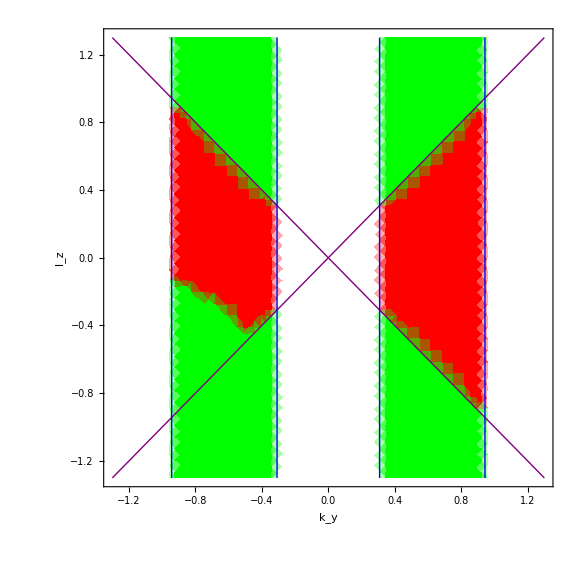
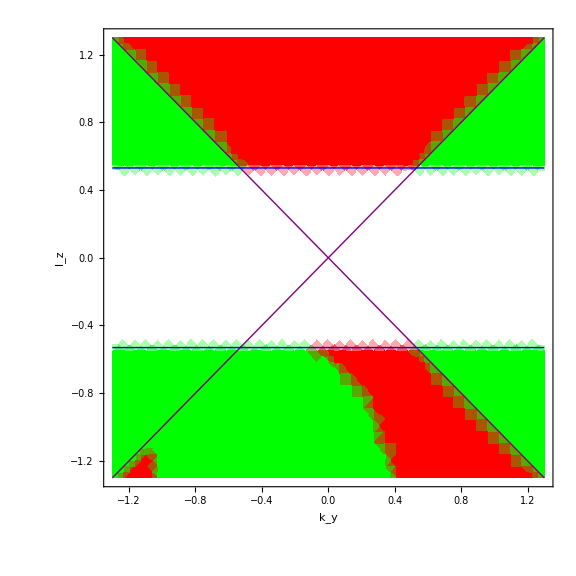
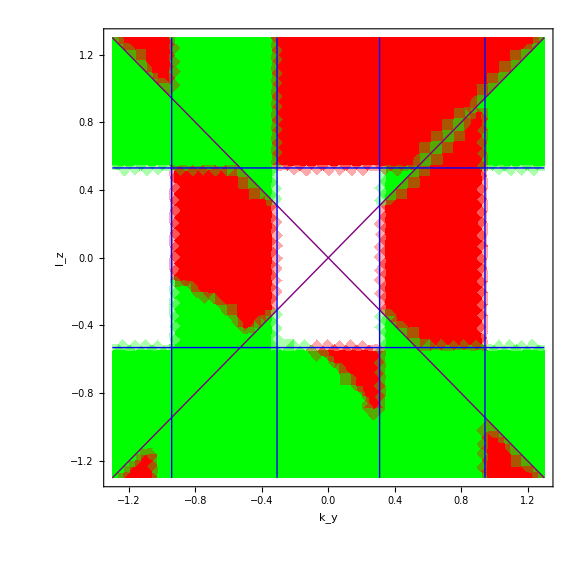
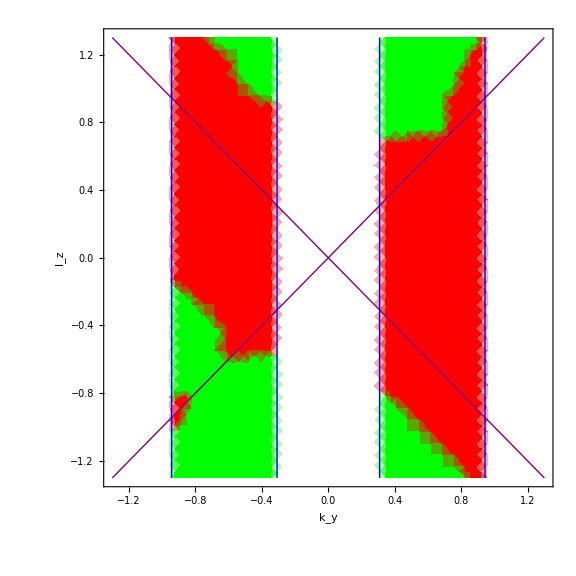
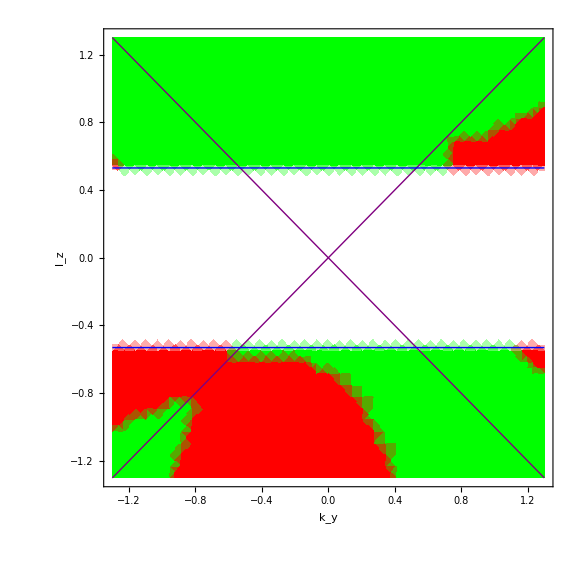
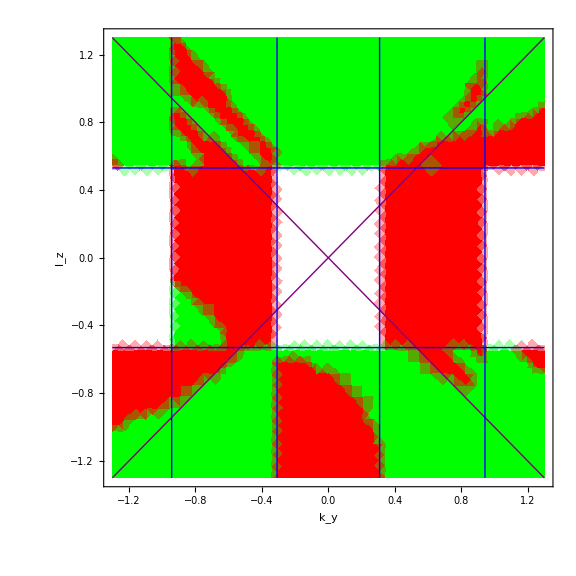
-Graphics-Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]
-Graphics-Im[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Im[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Im[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]

```mathematica
Grid[{
{
Labeled[Show[KLScanDensityPlotLxBReYZ,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotBxLReYZ,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotSumReYZ,AllThresholdLinesForKLScanInSumYZ,ImageSize->Large],"Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
},
{
Labeled[Show[KLScanDensityPlotLxBImYZ,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Im[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotBxLImYZ,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Im[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotSumImYZ,AllThresholdLinesForKLScanInSumYZ,ImageSize->Large],"Im[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
}
},ItemSize->{50,35}]
```

### Density heat map, with No deformation

Now Study the no-deformation case!

```mathematica
DensityForThisSection=20;
```

```mathematica
KLScanDensityPlotLxBReYZColouredNoDeformation=Block[
{},
DensityPlot[Log[Min[Max[Abs[Re[EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->1,DEBUG->False]]],1.0*^-3],1*^8]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,PlotRange->All,
Frame->True]
];
```

```mathematica
KLScanDensityPlotBxLReYZColouredNoDeformation=Block[
{},
DensityPlot[Log[Max[Abs[Re[EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,PlotRange->All,
Frame->True]
];
```

```mathematica
KLScanDensityPlotRealYZColouredNoDeformation=Block[
{},
DensityPlot[Log[Max[2Abs[Re[EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->0,DEBUG->False]]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,PlotRange->All,
Frame->True]
];
```

```mathematica
KLScanDensityPlotSumReYZColouredNoDeformation=Block[
{},
DensityPlot[Log[Min[Max[Abs[Re[
EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->1,DEBUG->False]+
EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]
],1.0*^-3],1.0*^5]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,PlotRange->All,
Frame->True]
];
```

```mathematica
KLScanDensityPlotAllReYZColouredNoDeformation=Block[
{},
DensityPlot[Log[Min[Max[Abs[Re[
EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->1,DEBUG->False]+
EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->2,DEBUG->False]+
2EvaluateCutForKLScanYZ[NoDeformationHookSemiInclusive,ky,lz,cutID->0,DEBUG->False]
]
],1.0*^-3],1.0*^5]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,PlotRange->All,
Frame->True]
];
```

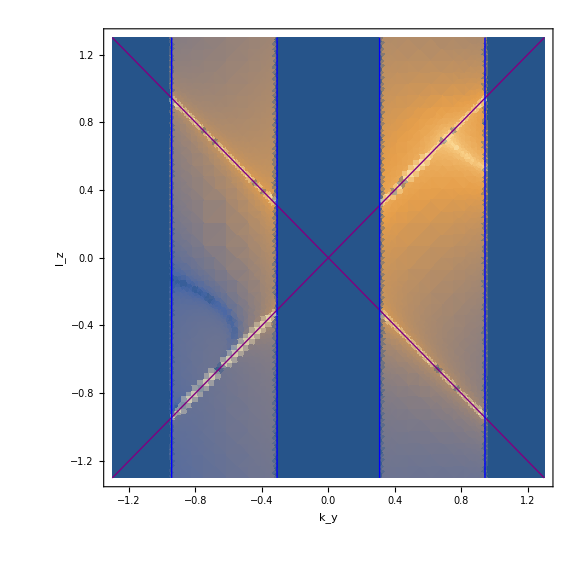
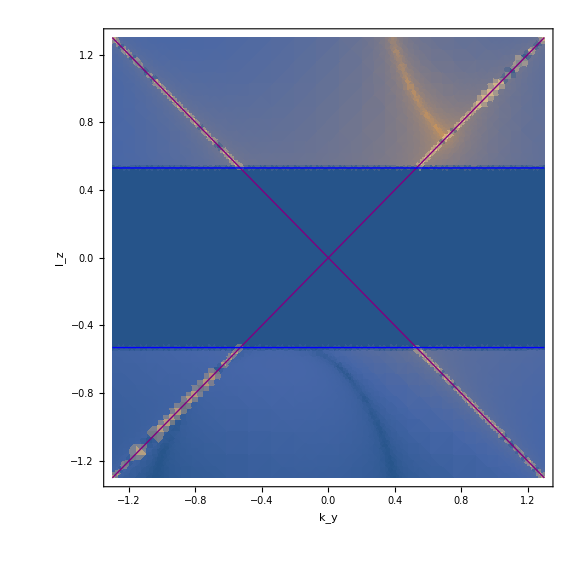
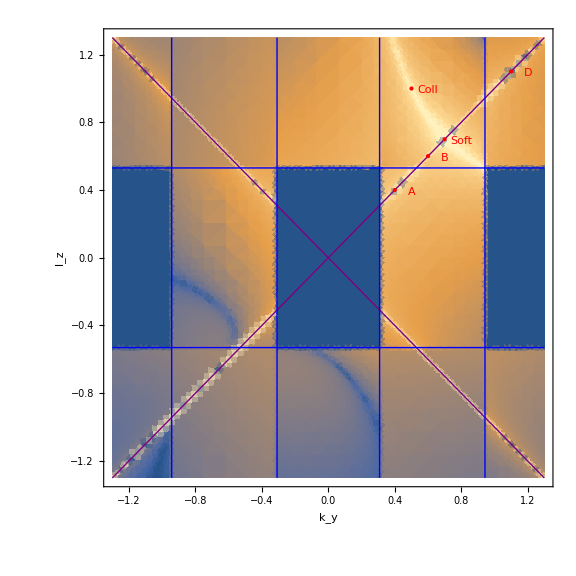
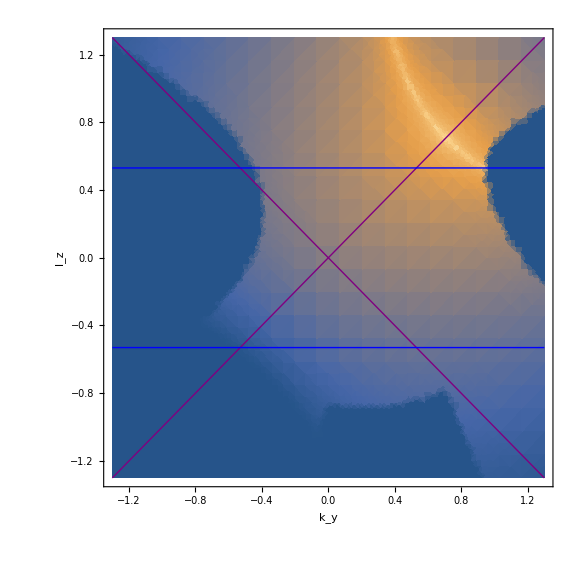
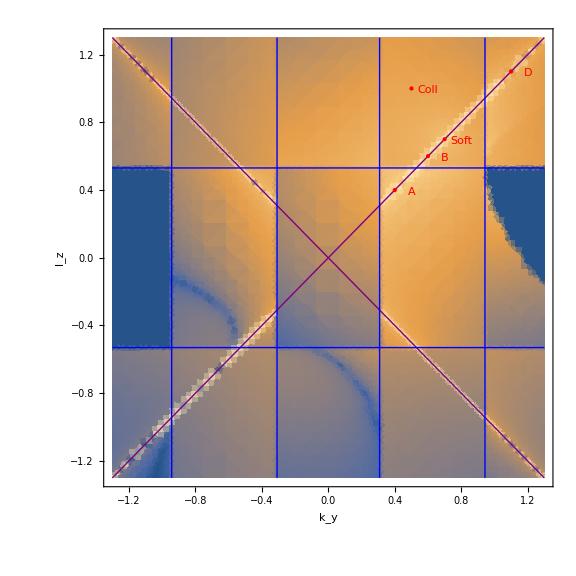
-Graphics-Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]
-Graphics-Real( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-Re[(LxB+BxL+Real)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] |

```mathematica
Grid[{
{
Labeled[Show[KLScanDensityPlotLxBReYZColouredNoDeformation,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotBxLReYZColouredNoDeformation,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[{KLScanDensityPlotSumReYZColouredNoDeformation,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]},
{
Labeled[Show[KLScanDensityPlotRealYZColouredNoDeformation,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Real( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[{KLScanDensityPlotAllReYZColouredNoDeformation,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Re[(LxB+BxL+Real)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
}
},ItemSize->{50,35}]
```

### Density heat map, with deformation

And now the same but with actual a full colour scale on the density plot

```mathematica
DensityForThisSection=20;
```

```mathematica
KLScanDensityPlotLxBReYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Re[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

```mathematica
KLScanDensityPlotLxBImYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Im[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

```mathematica
KLScanDensityPlotBxLReYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Re[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

```mathematica
KLScanDensityPlotBxLImYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Im[EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

```mathematica
KLScanDensityPlotSumReYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Re[
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]+
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]
],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

```mathematica
KLScanDensityPlotSumImYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Im[
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]+
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]]
],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

```mathematica
KLScanDensityPlotRealYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Re[2EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->0,DEBUG->False]]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

```mathematica
KLScanDensityPlotAllYZColoured=Block[
{},
DensityPlot[Log[Max[Abs[Re[
2EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->0,DEBUG->False]+
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->1,DEBUG->False]+
EvaluateCutForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,ky,lz,cutID->2,DEBUG->False]
]],1.0*^-3]],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->3,
Frame->True]
];
```

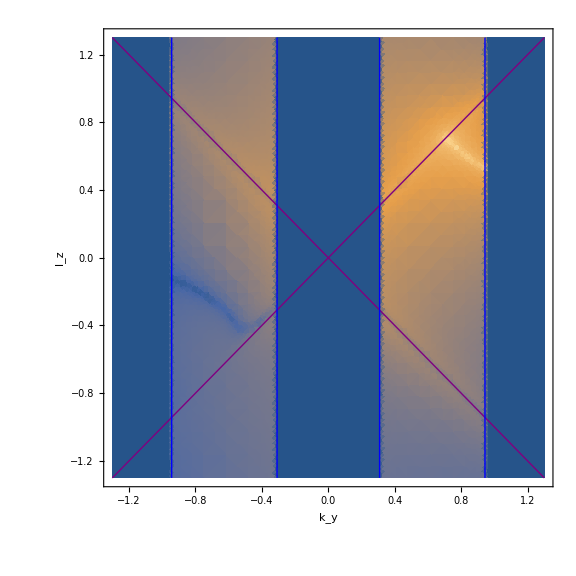
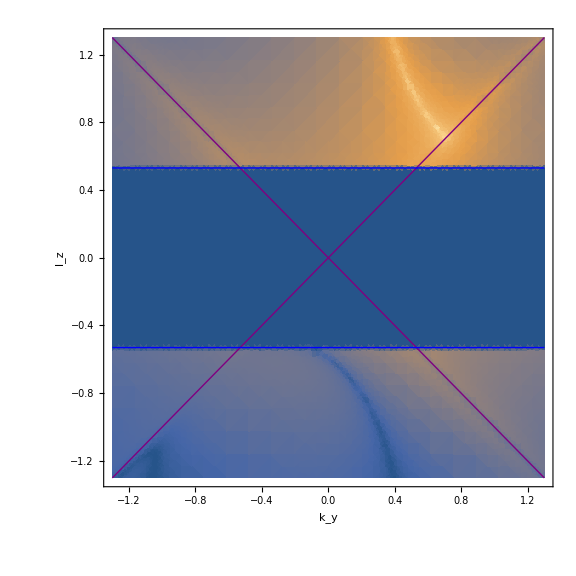
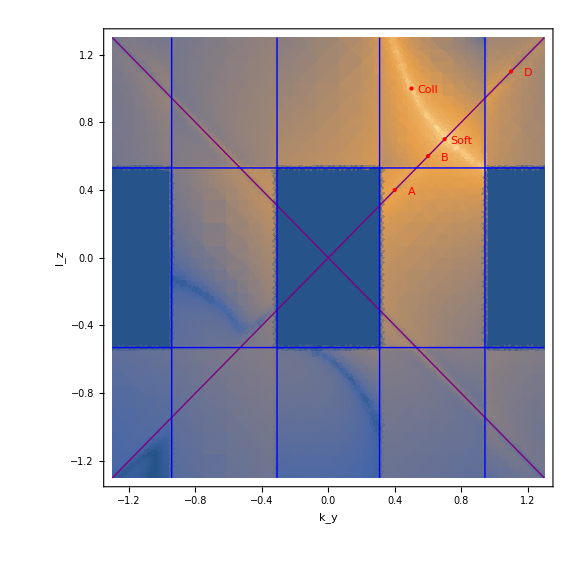
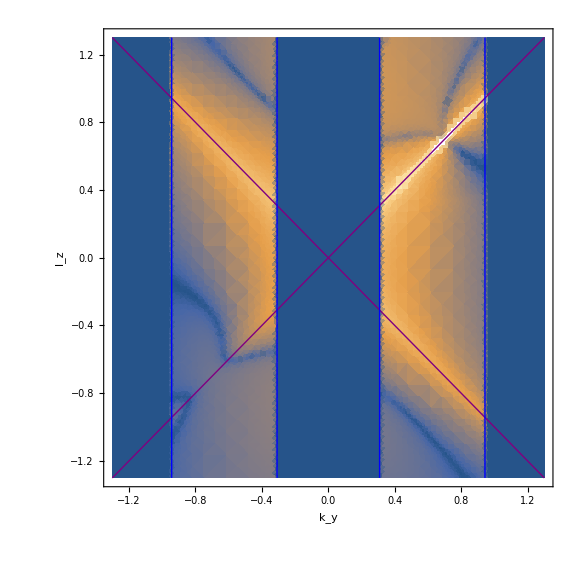
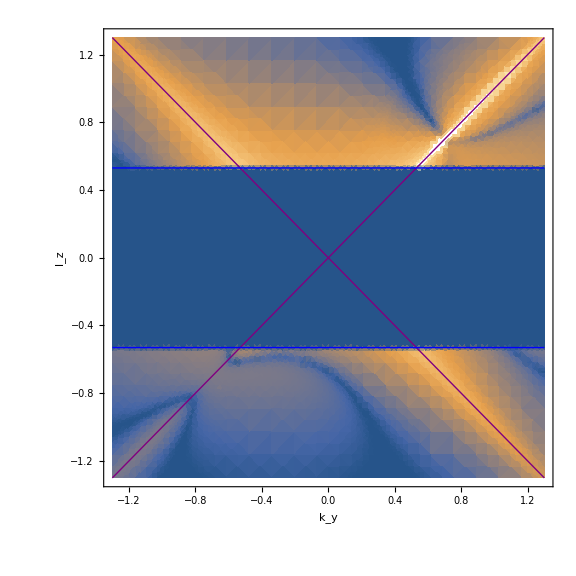
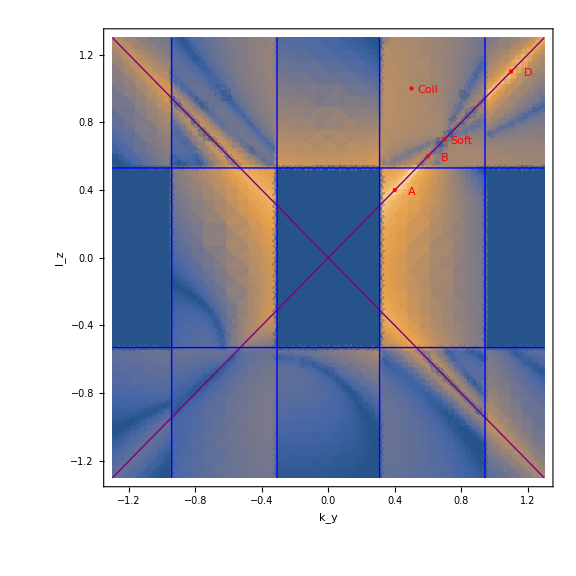
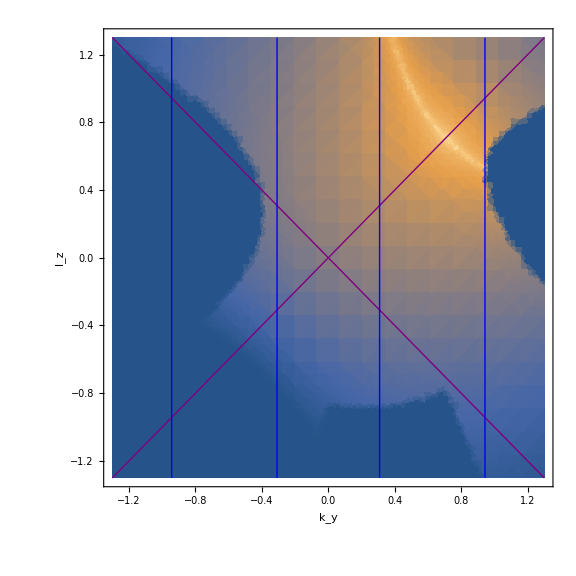
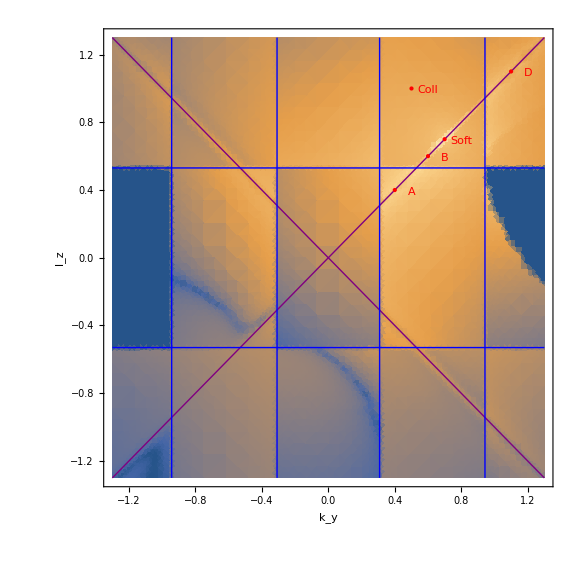
-Graphics-Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]
-Graphics-Im[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Im[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Im[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]
-Graphics-Real( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-Re[(LxB+BxL+Real)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] |

```mathematica
Grid[{
{
Labeled[Show[KLScanDensityPlotLxBReYZColoured,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotBxLReYZColoured,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[{KLScanDensityPlotSumReYZColoured,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
},
{
Labeled[Show[KLScanDensityPlotLxBImYZColoured,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Im[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotBxLImYZColoured,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Im[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[{KLScanDensityPlotSumImYZColoured,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Im[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
},
{
Labeled[Show[KLScanDensityPlotRealYZColoured,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Real( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[{KLScanDensityPlotAllYZColoured,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Re[(LxB+BxL+Real)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
}

},ItemSize->{50,35}]
```

### Scan along a line (0.2 , 0.2) → (1.1 , 1.1) + Δ

First look at individual points

```mathematica
ComputePoints[hook_,points_,labels_,OptionsPattern[{Delta->{0,10^-3},RotatedBasis->False,IncludeJacobian->False}]]:=Block[{LxBEval,BxLEval,REval,FullEval, RustEval,displacedPoint,header},
MyPrint["Δ = ( "<>ToString[OptionValue[Delta]⟦1⟧,InputForm]<>", "<>ToString[OptionValue[Delta]⟦2⟧,InputForm]<>" )"];
For[iPoint=1,iPoint≤Length[points],iPoint++,
displacedPoint=points⟦iPoint⟧+OptionValue[Delta];
REval=2EvaluateCutForKLScanYZ[hook,displacedPoint⟦1⟧,displacedPoint⟦2⟧,cutID->0,DEBUG->False,IncludeJacobian->OptionValue[IncludeJacobian],RotatedBasis->OptionValue[RotatedBasis]];
LxBEval=EvaluateCutForKLScanYZ[hook,displacedPoint⟦1⟧,displacedPoint⟦2⟧,cutID->1,DEBUG->False,IncludeJacobian->OptionValue[IncludeJacobian],RotatedBasis->OptionValue[RotatedBasis]];
BxLEval=EvaluateCutForKLScanYZ[hook,displacedPoint⟦1⟧,displacedPoint⟦2⟧,cutID->2,DEBUG->False,IncludeJacobian->OptionValue[IncludeJacobian],RotatedBasis->OptionValue[RotatedBasis]];
FullEval=EvaluateFullForKLScanYZ[hook,displacedPoint⟦1⟧,displacedPoint⟦2⟧,DEBUG->False,IncludeJacobian->OptionValue[IncludeJacobian],RotatedBasis->OptionValue[RotatedBasis]];
header="Point "<>labels⟦iPoint⟧<>" at ( "<>ToString[points⟦iPoint⟧⟦1⟧]<>", "<>ToString[points⟦iPoint⟧⟦2⟧]<>" ) + Δ :";
MyPrint[""];
MyPrint[header];
MyPrint[StringJoin[Table["-",{dummy,Range[StringLength[header]]}]]];
MyPrint["Real      = "<>If[Re[REval]≥0," ",""]<>ToString[REval,InputForm]];
MyPrint["LxB       = "<>If[Re[LxBEval]≥0," ",""]<>ToString[LxBEval,InputForm]];
MyPrint["BxL       = "<>If[Re[BxLEval]≥0," ",""]<>ToString[BxLEval,InputForm]];
MyPrint["LxB+BxL   = "<>If[Re[LxBEval+BxLEval]≥0," ",""]<>ToString[LxBEval+BxLEval,InputForm]];
MyPrint["LxB+BxL+R = "<>If[Re[LxBEval+BxLEval]≥0," ",""]<>ToString[LxBEval+BxLEval+REval,InputForm]];
MyPrint["Rust       = "<>If[Re[FullEval]≥0," ",""]<>ToString[FullEval,InputForm]];
];
MyPrint[""];
]
```

```mathematica
ComputePoints[
NoDeformationHookSemiInclusive,
{{0.4,0.4},{0.6,0.6},{0.7,0.7},{1.1,1.1},{0.5,1.}},
{"A","B","Soft","D","Collinear"},
Delta->{0,10^-3},RotatedBasis->True,IncludeJacobian->True
]
```

Δ = ( 0, 1/1000 )

Point A at ( 0.4, 0.4 ) + Δ :

-----------------------------

Real      =  12251.8294188296 + 0.*I

LxB       =  1.2862526528747303*^7 + 0.*I

BxL       =  0. + 0.*I

LxB+BxL   =  1.2862526528747303*^7 + 0.*I

LxB+BxL+R =  1.2874778358166132*^7 + 0.*I

Rust       =  1.287477835813429*^7 + 0.*I

Point B at ( 0.6, 0.6 ) + Δ :

-----------------------------

Real      =  46743.89648263286 + 0.*I

LxB       =  7.35833624522141*^6 + 0.*I

BxL       = -7.401929038936735*^6 + 0.*I

LxB+BxL   = -43592.793715325184 + 0.*I

LxB+BxL+R = 3151.102767307675 + 0.*I

Rust       =  3151.1027672983764 + 0.*I

Point Soft at ( 0.7, 0.7 ) + Δ :

--------------------------------

Real      =  812082.0963219771 + 0.*I

LxB       =  5.101834657689916*^6 + 0.*I

BxL       = -5.913748831945246*^6 + 0.*I

LxB+BxL   = -811914.1742553301 + 0.*I

LxB+BxL+R = 167.92206664697733 + 0.*I

Rust       =  167.92206901649507 + 0.*I

Point D at ( 1.1, 1.1 ) + Δ :

-----------------------------

Real      =  5573.600114146579 + 0.*I

LxB       =  0. + 0.*I

BxL       = -4.510696484117176*^6 + 0.*I

LxB+BxL   = -4.510696484117176*^6 + 0.*I

LxB+BxL+R = -4.50512288400303*^6 + 0.*I

Rust       = -4.505122884003028*^6 + 0.*I

Point Collinear at ( 0.5, 1. ) + Δ :

------------------------------------

Real      =  5.220262461497726*^9 + 0.*I

LxB       =  9728.643379174313 + 0.*I

BxL       = -5.220267880654676*^9 + 0.*I

LxB+BxL   = -5.220258152011297*^9 + 0.*I

LxB+BxL+R = 4309.4864292144775 + 0.*I

Rust       =  4309.558668713625 + 0.*I

```mathematica
RefreshHooks[]
```

{True,True,True,True}

```mathematica
Plot[
{
Log[Max[Abs[Re[EvaluateFullForKLScanYZ[DeformUVDampenAfterLambda10HookSemiInclusive,1/Sqrt[2]-t,1/Sqrt[2]+t,DEBUG->False,IncludeJacobian->True,RotatedBasis->True]]],1.0*^-1]]
}
,{t,-0.1,0.1},PlotLabels->{"Rust"},PlotPoints->10,MaxRecursion->4,ImageSize->Large
]
```

-Graphics-

Now at plots:

```mathematica
MakeApproachPlot[hook_,point_,OptionsPattern[{Phase->Re,IncludeJacobian->False,RotatedBasis->False}]]:=Block[{
},
Plot[
{
Log[Max[Abs[2OptionValue[Phase][EvaluateCutForKLScanYZ[hook,point⟦1⟧+10^-t ,point⟦2⟧-10^-t,cutID->0,DEBUG->False]]],1.0*^-1]],
Log[Max[Abs[OptionValue[Phase][EvaluateCutForKLScanYZ[hook,point⟦1⟧+10^-t,point⟦2⟧-10^-t,cutID->1,DEBUG->False]]],1.0*^-1]],
Log[Max[Abs[OptionValue[Phase][EvaluateCutForKLScanYZ[hook,point⟦1⟧+10^-t,point⟦2⟧-10^-t,cutID->2,DEBUG->False]]],1.0*^-1]],
Log[Max[Abs[
(2OptionValue[Phase][EvaluateCutForKLScanYZ[hook,point⟦1⟧+10^-t ,point⟦2⟧-10^-t,cutID->0,DEBUG->False]]+
OptionValue[Phase][EvaluateCutForKLScanYZ[hook,point⟦1⟧+10^-t,point⟦2⟧-10^-t,cutID->1,DEBUG->False]]+
OptionValue[Phase][EvaluateCutForKLScanYZ[hook,point⟦1⟧+10^-t ,point⟦2⟧-10^-t,cutID->2,DEBUG->False]])
],1.0*^-1]],
Log[Max[Abs[OptionValue[Phase][EvaluateFullForKLScanYZ[hook,point⟦1⟧+10^-t,point⟦2⟧-10^-t,DEBUG->False,IncludeJacobian->False]]],1.0*^-1]]
(*,
OptionValue[Phase][
EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->1,DEBUG->False]
+EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->2,DEBUG->False]
]*)
}
,{t,0.5,3},PlotLabels->{"Real","LxB","BxL","Total","Rust"},PlotPoints->10,MaxRecursion->4,ImageSize->Large
]
]
```

```mathematica
(* MakeApproachPlot[DeformUVDampenAfterLambda10HookSemiInclusive,{0.6,0.8}] *)
```

```mathematica
AllPlotsDeformationIm=Table[Labeled[MakeApproachPlot[DeformUVDampenAfterLambda10HookSemiInclusive,point⟦2⟧,Phase->Im],point⟦1⟧],{point,{
{"A",{0.4,0.4}},
{"B",{0.6,0.6}},
{"Soft",{1/Sqrt[2],1/Sqrt[2]}},
{"C",{1.1,1.1}},
{"Collinear",{0.5,1.}}
}}];
```

```mathematica
Grid[ArrayReshape[Table[Show[p],{p,AllPlotsDeformationIm}],{2,3}],ItemSize->{55,25}]
```

-Graphics-A | -Graphics-B | -Graphics-Soft
-Graphics-C | -Graphics-Collinear | 0

```mathematica
RefreshHooks[]
```

{True,True,True,True}

```mathematica
AllPlotsDeformation=Table[Labeled[MakeApproachPlot[DeformUVDampenAfterLambda10HookSemiInclusive,point⟦2⟧],point⟦1⟧],{point,{
{"A",{0.4,0.4}},
{"B",{0.6,0.6}},
{"Soft",{1/Sqrt[2],1/Sqrt[2]}},
{"C",{1.1,1.1}},
{"Collinear",{0.5,1.}}
}}];
```

```mathematica
ComputePoints[
DeformUVDampenAfterLambda10HookSemiInclusive,
{N[{1/Sqrt[2],1/Sqrt[2]}]},
{"UltraSoft"},
Delta->{10^-2,-10^-2}
]
```

Δ = ( 1/100, -1/100 )

Point UltraSoft at ( 0.707107, 0.707107 ) + Δ :

-----------------------------------------------

Real      =  3.656479614914188*^10 + 0.*I

LxB       = -3.65652789913092*^10 - 0.0337133861569403*I

BxL       =  483683.5507286718 - 35.21396929250422*I

LxB+BxL   = -3.656479530775847*^10 - 35.24768267866116*I

LxB+BxL+R = 841.3834075927734 - 35.24768267866116*I

Rust       =  0. + 0.*I

```mathematica
Grid[ArrayReshape[Table[Show[p],{p,AllPlotsDeformation}],{2,3}],ItemSize->{55,25}]
```

-Graphics-A | -Graphics-B | -Graphics-Soft
-Graphics-C | -Graphics-Collinear | 0

```mathematica
Grid[ArrayReshape[Table[Show[p],{p,AllPlotsDeformation}],{2,3}],ItemSize->{55,25}]
```

-Graphics-A | -Graphics-B | -Graphics-Soft
-Graphics-C | -Graphics-Collinear | 0

```mathematica
AllPlotsNoDeformation=Table[Labeled[MakeApproachPlot[NoDeformationHookSemiInclusive,point⟦2⟧],point⟦1⟧],{point,{
{"A",{0.4,0.4}},
{"B",{0.6,0.6}},
{"Soft",{1/Sqrt[2],1/Sqrt[2]}},
{"C",{1.1,1.1}},
{"Collinear",{0.5,1.}}
}}];
```

```mathematica
Grid[ArrayReshape[Table[Show[p],{p,AllPlotsNoDeformation}],{2,3}],ItemSize->{55,25}]
```

-Graphics-A | -Graphics-B | -Graphics-Soft
-Graphics-C | -Graphics-Collinear | 0

```mathematica
ArrayReshape[{1,2,3,4,5},{2,3}]
```

(1 | 2 | 3
4 | 5 | 0)

```mathematica
MakePlot[hook_,deltaKy_,deltaLz_,OptionsPattern[{Phase->Re}]]:=Block[{
minKy=0.0,minLz=0.0,
maxKy=1.0,maxLz=1.0
},
Plot[
{
2OptionValue[Phase][EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->0,DEBUG->False]],
OptionValue[Phase][EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->1,DEBUG->False]],
OptionValue[Phase][EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->2,DEBUG->False]](*,
OptionValue[Phase][
EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->1,DEBUG->False]
+EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->2,DEBUG->False]
]*)
}
,{t,0,1.1},PlotLabels->{"Real","LxB","BxL"}, PlotRange->{Automatic,{-10^4,10^4}}(*,PlotPoints->5,MaxRecursion->3*)
]
]
```

```mathematica
MakeLogPlot[hook_,deltaKy_,deltaLz_,OptionsPattern[{Phase->Re}]]:=Block[{
minKy=0.0,minLz=0.0,
maxKy=1.0,maxLz=1.0
},
LogPlot[
{
Abs[Min[2OptionValue[Phase][EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->0,DEBUG->False]],1.0*^-5]],
Abs[Min[OptionValue[Phase][EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->1,DEBUG->False]],1.0*^-5]],
Abs[Min[OptionValue[Phase][EvaluateCutForKLScanYZ[hook,deltaKy+minKy+(maxKy-minKy)t,deltaLz+minLz+(maxLz-minLz)t,cutID->2,DEBUG->False]],1.0*^-5]]
}
,{t,0.,1.1},PlotLabels->{"Real","LxB","BxL"} (*,PlotRange->{Automatic,{-10^4,10^4}},PlotPoints->5,MaxRecursion->3*)
]
]
```

```mathematica
(*MakePlot[NoDeformationHookSemiInclusive,0.05,0]*)
```

## Plots of deformation magnitude and integrands

Some 1D plots along particular directions

```mathematica
RFM$KillAllHooks[];
DeformUVDampenAfterLambda10Hook=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/deform_UV_dampen_after_constant_lambda10.yaml",
DEBUG->False
];
RFM$CheckHookStatus[DeformUVDampenAfterLambda10Hook]
```

True

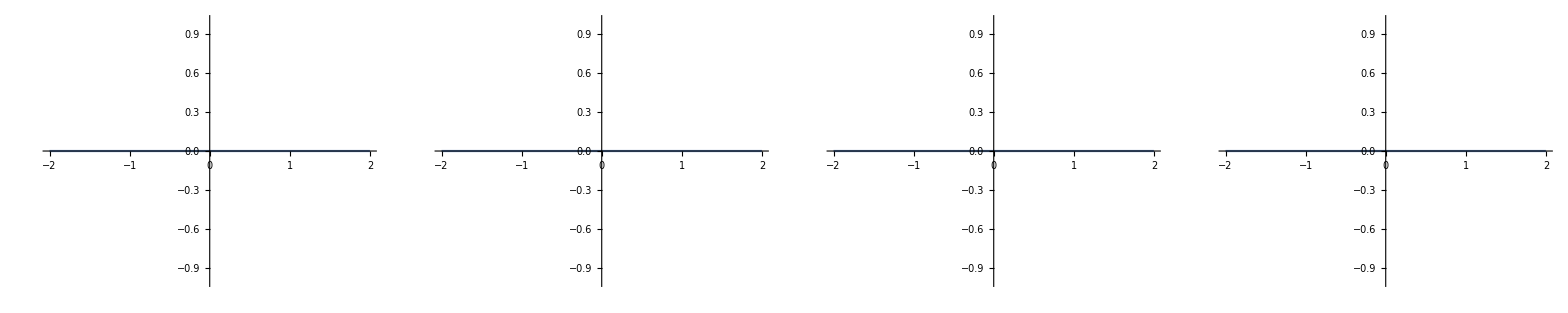

```mathematica
(* Uncomment below to refresh the hook everytime you make changes *)
RFM$KillAllHooks[];
DeformUVDampenAfterLambda10Hook=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/deform_UV_dampen_after_constant_lambda10.yaml",
DEBUG->False
];
Block[{
ApproachDirections={{0,1},{1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],-1/Sqrt[2]},{1,0}}
},
Grid[{Table[
Plot[Norm[(GetDeformationVectorXY@@(SoftPoint⟦;;2⟧+t ApproachDirection))],{t,-2,2}],
{ApproachDirection,ApproachDirections}]}]
]
```

Some 3D plot now

```mathematica
Plot3D[Log[Norm[(EvaluateFullXY[DeformUVDampenAfterLambda10Hook,#1,#2]&)@@(SoftPoint⟦;;2⟧+{kx,ky})]],{kx,-0.1,0.1},{ky,-0.1,0.1},PlotPoints->3]
```

-Graphics3D-

## Numerical integration with Mathematica

```mathematica
LTDIntegrand[x1_?NumberQ,x2_?NumberQ,x3_?NumberQ,x4_?NumberQ,x5_?NumberQ,x6_?NumberQ]:=Re[RFM$EvaluateIntegrand[NoDeformationHook,{x1,x2,x3,x4,x5,x6},DEBUG->False]];
```

```mathematica
PerformNumericalIntegration[stats_]:=Module[
{ThisIntegrand ,IntermediateResult=0,
rBoundMin=0.001,rBoundMax=0.999,
BoundMin=0.0,BoundMax=1.0
(*MCPoints={};*)
},
Association[Table[
IntermediateResult=NIntegrate[
LTDIntegrand[x1,x2,x3,x4,x5,x6],
{x1,rBoundMin,rBoundMax},{x2,BoundMin,BoundMax},{x3,BoundMin,BoundMax},
{x4,rBoundMin,rBoundMax},{x5,BoundMin,BoundMax},{x6,BoundMin,BoundMax},
Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->statistics,MaxRecursion->1000
(*,EvaluationMonitor:>AppendTo[MCPoints,{{x1,x2,x3,x4,x5,x6},RealCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False],VirtualCutRescalingIntegrand[{x1,x2,x3,x4,x5,x6},0,2,False]}]*)
];
Print["Result for "<>ToString[statistics]<>" sample points: "<>ToString[IntermediateResult]];
statistics->IntermediateResult,{statistics, stats}]
]
]
```

```mathematica
NumericalIntegrationResults=PerformNumericalIntegration[{100,1000}]
```

<|100→823.499,1000→965.022,10000→821.089,30000→909.878|>

```mathematica
ComplexPlot
```

```mathematica
ComplexPlot3D[(z^2+1)/(z^2-1),{z,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics3D-